```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jenna/jennaproject/mma

```mathematica
Needs["Integrals`"]
Needs["PlotLegends`"]
```

Needs::nocont: Context Integrals` was not created when Needs was evaluated.

```mathematica
mp0=Import["../data/test_matterPower_0.dat","Table"];
trlist=Import["../data/Tru_Tm.txt","Table"];
h=0.703;
```

```mathematica
size=Dimensions[mp0][[1]]
α=Log[mp0[[2,1]]/mp0[[1,1]]]/Log[mp0[[2,2]]/mp0[[1,2]]]
β=Log[mp0[[size,2]]/mp0[[size-1,2]]]/Log[mp0[[size,1]]/mp0[[size-1,1]]]
```

496

1.03608

-2.44708

```mathematica
Pm=Interpolation[mp0];
tr=Interpolation[trlist];
```

```mathematica
Dimensions[trlist]
```

{140,2}

```mathematica
Pmgood[k_]:=If[k<0.0001||k>1.993,0,Pm[k]];
Trgood[k_]:=If[k<1.9755223192*^-7||k>12.477498542,0,tr[k]];
```

```mathematica
Plot[(1+r^2)/(2r),{r,0,5}];
```

```mathematica
Limit[(r-μ)/(1+r^2-2r*μ)^(1/2),r->1]/.μ->1
```

0

```mathematica
Limit[(3r+7μ-10r*μ^2)/(14*r*(1+r^2-2r*μ)),r->1]/.μ->1
```

13/28

```mathematica
kvals=Union[0.001*Range[5,99],0.01*Range[1,30]];
Dimensions[kvals]
```

{116}

```mathematica
(*Clear[S]
S=#^3/(2*Pi^2)*(fgps[#,Pmgood]+fgps2[#,Pmgood])&/@Take[kvals,{1,60,4}];*)
```

```mathematica
aru=#^3/(2*Pi^2)*autoru[#,Pmgood,Trgood]&/@Take[kvals,{1,116,4}];
anl=#^3/(2*Pi^2)*autonl[#,Pmgood]&/@Take[kvals,{1,116,4}];
crs=#^3/(2*Pi^2)*cross[#,Pmgood,Trgood]&/@Take[kvals,{1,116,4}];
```

Suave::success: Needed 19000 function evaluations on 19 subregions.

Suave::success: Needed 43000 function evaluations on 43 subregions.

Suave::success: Needed 23000 function evaluations on 23 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 27000 function evaluations on 27 subregions.

Suave::success: Needed 37000 function evaluations on 37 subregions.

Suave::success: Needed 45000 function evaluations on 45 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

Suave::success: Needed 22000 function evaluations on 22 subregions.

Suave::success: Needed 50000 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

```mathematica
mark1=Graphics[{Blue,Disk[]}];
mark2=Graphics[{Red,Disk[]}];
mark3=Graphics[{Orange,Disk[]}];
```

```mathematica
γ1=ListLogLogPlot[Thread[{Take[kvals,{1,116,4}],Abs[aru]/h^3}],PlotRange->{{0.005,0.3},{10,10^4}},PlotMarkers-> {mark1, .02}];
γ2=ListLogLogPlot[Thread[{Take[kvals,{1,116,4}],Abs[anl]/h^3}],PlotRange->{{0.005,0.3},{10,10^4}},PlotMarkers-> {mark2, .02}];
γ3=ListLogLogPlot[Thread[{Take[kvals,{1,116,4}],Abs[crs]/h^3}],PlotRange->{{0.005,0.3},{10,10^4}},PlotMarkers-> {mark3, .02}, AxesLabel->{a,b}];
(*γall=ListLogLogPlot[Thread[Take[kvals,{1,60,4}],S/h^3}],PlotRange->{{0.005,0.3},{10,10^5}},PlotStyle->{Thick,Red},Frame->True]*)
```

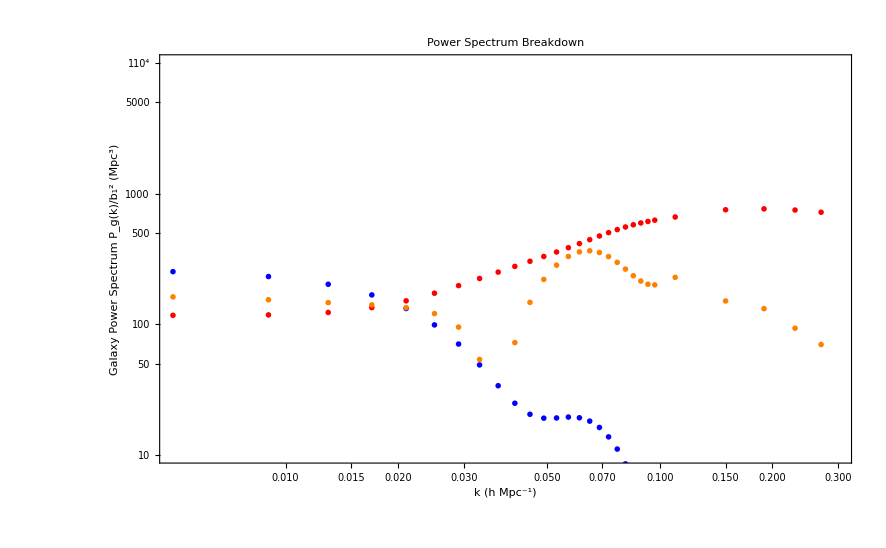

```mathematica
Show[γ1,γ2,γ3,PlotLabel->"Power Spectrum Breakdown",BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True, FrameLabel->{"k (h Mpc^-1)","Galaxy Power Spectrum P_g(k)/b_1^2 (Mpc^3)"},RotateLabel->True](*PlotLegend->{"Relative velocity","Nonlinear bias","Cross power spectrum"}]*)
```

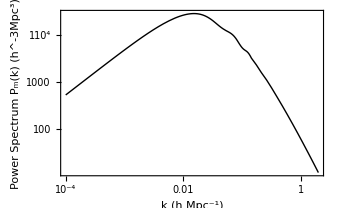

```mathematica
pwr=LogLogPlot[Pmgood[x],{x,0.0001,2},BaseStyle->{FontFamily->"Helvetica",FontSize->10},
Frame->True, FrameLabel->{"k (h Mpc^-1)","Power Spectrum P_m(k) (h^-3Mpc^3)"},RotateLabel->True,PlotStyle->{Thick,Black}]
```

```mathematica
Export["~/jennaproject/figs/Pm.pdf",pwr];
```